# IMRPhenomD Defs

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

This tutorial shows the final steps to fully define the IMRPhenomD waveform:

```mathematica
PacletDirectoryLoad["/Users/felipe/Documents/GitHub"]
```

{/Users/felipe/Documents/GitHub}

```mathematica
<<FelipeBarbosa`SymDALI`
```

It is useful to import our rules developed inIMRPhenomD Rules,so we can see which heads were used and define our functions considering that:

```mathematica
{SymRules, NRules} = DerivativeRulesLoad["IMRPhenomD"];
```

What interests us are the Keys, or rather the symbols for which there are definitions:

```mathematica
Keys@SymRules
```

{ϕIns,ϕInt,ϕMR,α5,𝒜Ins,𝒜Int,v2,𝒜MR,γ2,SpecialFrequencies,ωDAMPING,ωRD,γ3}

In general the total phase and amplitude is:

```mathematica
HoldForm[ϕIMR== ϕIns θ[0.018-ω] + ϕInt θ[(ω-0.018) (ωRD/2 - ω)] +ϕMR θ[ω-ωRD/2]]
HoldForm[𝒜IMR== 𝒜Ins θ[0.014-ω] + 𝒜Int θ[(ω-0.014) (ωPeak - ω)] +AMR θ[(ω-ωPeak)  (0.2-ω)]]
```

ϕIMR==ϕIns θ[0.018-ω]+ϕInt θ[(ω-0.018) (ωRD/2-ω)]+ϕMR θ[ω-ωRD/2]

𝒜IMR==𝒜Ins θ[0.014-ω]+𝒜Int θ[(ω-0.014) (ωPeak-ω)]+AMR θ[(ω-ωPeak) (0.2-ω)]

However some of these phases and amplitudes have additional definitions, which we shall work out along the way.

Lastly, we shall compare our definitions against the Ripple package, which is known to agree with the LIGO implementation.  For that, we need a Python session:

```mathematica
python = StartExternalSession[
	{

		"System" -> "Python"
    }
];
```

```mathematica
ExternalEvaluate[python, {
	   "import numpy as np",
            "from ripplegw.waveforms import IMRPhenomD as IMRD",
            "from ripplegw.waveforms import IMRPhenomD_utils as IMRD_utils"
       }]
```

{Null,Null,Null}

It will also be convenient to organize the necessary rules for evaluation in a list:

```mathematica
Module[
	{allVars, takeVars, compiledFunctions, extra},
	
	takeVars[x_] := (List@@x)/. q_Pattern :> q[[1]];
	
	rulesList  = NRules/@(Keys@NRules);

	rulesList = Flatten[rulesList[[All,1;;5]]];
	
	allVars = takeVars /@ rulesList[[All, 1]];

	compiledFunctions = MapThread[
   			#[Sequence @@ #2] &,
   			{rulesList[[All, 2]], allVars }
   		];
	
	rulesList = MapThread[
   		#1 -> #2 &,
   		{rulesList[[All, 1]], compiledFunctions}
   	];

	(*We will need this extra one for the amplitude:*)
	extra = $D[{0,0,0,0,1,0},AMR][ω_,η_,χPN_,γ3ωDAMP_,ΔωRD_,γ2_]->CompiledFunction[…][ω,η,χPN,γ3ωDAMP,ΔωRD,γ2];
	AppendTo[rulesList, extra];

	rulesList = Dispatch[rulesList];

]
```

## Phase

ϕIns and ϕInt are functions of fundamental quantities:

```mathematica
NRules[#][[1,1]]&/@{"ϕIns", "ϕInt"}
```

{ϕIns[ω_,η_,χ1_,χ2_],ϕInt[ω_,η_,χPN_]}

However, ϕMR, is a function of other functions (ωRD, ωDAMP ∧ α5):

```mathematica
NRules["ϕMR"][[1,1]]
```

ϕMR[ω_,η_,χPN_,ωRD_,ωDAMP_,α5_]

We recall from, IMRPhenomD Rules (Special Frequencies section) that ωRD ∧ ωDAMP stand for interpolation functions:

```mathematica
HoldForm@(ringdownFrequency = SpecialFrequencies[η,S, ωRD[aeff[η,S]]])
HoldForm@(DampingFrequency = SpecialFrequencies[η,S, ωDAMP[aeff[η,S]]])
```

ringdownFrequency=SpecialFrequencies[η,S,ωRD[aeff[η,S]]]

DampingFrequency=SpecialFrequencies[η,S,ωDAMP[aeff[η,S]]]

Recalling the definitions:

```mathematica
NRules[#][[1,1]]&/@{"SpecialFrequencies", "ωRD", "ωDAMPING", "α5"}
```

{SF[η_,S_,inter_],ωRD[x_],ωDAMP[x_],α5[η_,χPN_]}

This motivates the definition:

```mathematica
ϕtotal1[ω_, η_, χ1_, χ2_, χPN_, S_] = Module[{
	aeff = S + 2 √3. η + (-0.085 S + 0.102 S^2 - 1.355 S^3-0.868 S^4) η - 4.399 η^2+(-5.837 S-2.097 S^2+4.109 S^3+2.064 S^4) η^2+9.397 η^3-13.181 η^4,
	ringdownFrequency, DampingFrequency, α
	},

	ringdownFrequency = SF[η, S, ωRD[aeff]];
	DampingFrequency = SF[η,S, ωDAMP[aeff]];
	α= α5[η,χPN];

	 (
		ϕIns[ω, η, χ1, χ2] usθ[0.018 - ω] + 
		ϕInt[ω, η, χPN] usθ[(ringdownFrequency/2 - ω) (ω-0.018)] +
		ϕMR[ω, η, χPN, ringdownFrequency, DampingFrequency, α] usθ[ω - ringdownFrequency/2]
	)
];
```

```mathematica
NRules[#][[1,1]]&/@{"ϕIns", "ϕInt", "ϕMR"}
```

{ϕIns[ω_,η_,χ1_,χ2_],ϕInt[ω_,η_,χPN_],ϕMR[ω_,η_,χPN_,ωRD_,ωDAMP_,α5_]}

Where ϕtotal1 stands from the fact that this is not yet the full phase. We still need the C(1) terms:

```mathematica
C1[ω_, η_, χ1_, χ2_, χPN_, S_] = Module[{
	aeff = S + 2 √3. η+ (-0.085 S+0.102 S^2 - 1.355 S^3-0.868 S^4) η - 4.399 η^2+(-5.837 S-2.097 S^2+4.109 S^3+2.064 S^4) η^2+9.397 η^3-13.181 η^4,
	ringdownFrequency, DampingFrequency, α,
	δβ0, δβ1, δα0, δα1
	},
	
	ringdownFrequency = SF[η, S, ωRD[aeff]];
	DampingFrequency = SF[η,S, ωDAMP[aeff]];
	α= α5[η,χPN];

	δβ1 =(
		$D[{1,0,0,0}, ϕIns][0.018, η, χ1, χ2] - 
		$D[{1,0,0}, ϕInt][0.018, η, χPN]
	);

	δβ0 = ϕIns[0.018, η, χ1, χ2] - ϕInt[0.018, η, χPN] - δβ1 0.018;

	δα1 = (
		$D[{1,0,0}, ϕInt][ringdownFrequency/2, η, χPN] + δβ1- 
		$D[{1,0,0,0,0,0},ϕMR][ringdownFrequency/2, η, χPN, ringdownFrequency, DampingFrequency, α]
	);

	δα0 = (
		ϕInt[ringdownFrequency/2, η, χPN] + δβ1 ringdownFrequency/2 + δβ0 - 
		ϕMR[ringdownFrequency/2, η, χPN, ringdownFrequency, DampingFrequency, α] - δα1 ringdownFrequency/2
	);

	(δβ0 + δβ1 ω) usθ[(ringdownFrequency/2 - ω) (ω-0.018)] + (δα0 + δα1 ω) usθ[ω - ringdownFrequency/2]
];
```

So the first phase reads:

```mathematica
ϕIMR[ω_, η_, χ1_, χ2_, χPN_, S_] =(
	ϕtotal1[ω, η, χ1, χ2, χPN, S] + C1[ω, η, χ1, χ2, χPN, S]
)//Simplify[#, ComplexityFunction->ByteCount]&;
```

We are still not done, the complete phase reads:

```mathematica
"Ψ[ω,...] = ϕIMR[ω, ...] - ϕIMR[ωref,...] - 2ϕc + 2 π tc f + t0 (fref-f),"
"t0 ≡ ∂_ω ϕMR[ωPeak,...]"
```

Ψ[ω,...] = ϕIMR[ω, ...] - ϕIMR[ωref,...] - 2ϕc + 2 π tc f + t0 (fref-f),

t0 ≡ ∂_ω ϕMR[ωPeak,...]

We still need to define ωPeak:

```mathematica
ωPeak[ringdownFrequency_, DampingFrequency_, γ2_, γ3_] :=If[
	γ2<=1,	
	ringdownFrequency + (DampingFrequency γ3 (√(1-γ2^2) -1))/γ2,
	ringdownFrequency - (γ3 DampingFrequency)/γ2
]
```

Now we can define the full phase, which will depend on the basic variables, meaning that we will be eliminating S,  χPN and ω:

```mathematica
Ψ[f_, M_, η_, χ1_, χ2_, ϕc_, tc_, fref_]  := Module[
	{
		ringdownFrequency, DampingFrequency, PeakFrequency,S, χPN, χs = (χ1+χ2)/2, χa = (χ1-χ2)/2,
		G = UnitConvert[("GravitationalConstant")/("SpeedOfLight")^3, ("Seconds")/("SolarMass")][[1]], ω,aeff, peakFrequency, ωref,
		t0, α, gamma2, gamma3
	},
	
	χPN = √(1- 4 η) χa + (1-(76 η)/113) χs;
	S =  1/4 (1 + √(1-4 η))^2 (χs+χa)+1/4 (1-√(1-4 η))^2 (χs-χa);
	(*Make some conventions:*)
	aeff = S + 2 √3. η+(-0.085 S+0.102 S^2 - 1.355 S^3-0.868 S^4) η - 4.399 η^2+(-5.837 S-2.097 S^2+4.109 S^3+2.064 S^4) η^2+9.397 η^3-13.181 η^4;
	
	ω = G M f;
	ωref = G M fref;
	
	ringdownFrequency = SF[η, S, ωRD[aeff]];
	DampingFrequency = SF[η, S, ωDAMP[aeff]];
	α= α5[η,χPN];
	gamma2 = γ2[η, χPN];
	gamma3 = γ3[η, χPN];

	peakFrequency = ωPeak[ringdownFrequency, DampingFrequency, gamma2, gamma3];

	t0 =  $D[{1,0,0,0,0,0}, ϕMR][
			peakFrequency,
			η, 
			χPN,
			ringdownFrequency,
			DampingFrequency,
			α
		];


	(*Now, we can Finally write the symbolic expression:*)
	ϕIMR[ω, η, χ1, χ2, χPN, S] - ϕIMR[ωref, η, χ1, χ2, χPN, S]  - t0 (ω - ωref) -  2 ϕc + 2 π tc f
](*//Simplify[
	#, 
	ComplexityFunction->ByteCount, 
	Assumptions-> 0<η<1/4 &&M>0 && -1<=χ1 <=1 && -1<=χ2 <=1 && f>0 &&fref>0
]&;*)
```

ϕIMR[$f, $η, $χ1, $χ2, $χPN, $S]

It would be wise to compare this rather large and complicated function against an answer we know to be right:

```mathematica
helperCoeffs = ExternalFunction[python, "def Coeffs(theta):
	a = IMRD_utils.get_coeffs(theta)
	return np.array(a)"
];

RippleCoeffs[θ_] := helperCoeffs[θ]//Normal

helperArg = ExternalFunction[python, "def h0(f, θin, θextr, coeffs,  fref):
	b = np.array(f)
	a = IMRD._gen_IMRPhenomD(b, θin, θextr, coeffs,  fref)
	return np.array(a)"
];
(*the function takes the arguments: Mc, eta, chi1, chi2, dist_mpc, tc, phic, inclination*)
Argument[f_, θin_,θex_, coeffs_, fref_] := Arg[helperArg[f, θin, θex, coeffs, fref]//Normal](*we only need hp for the phase.*)
```

Now, we go for a test:

```mathematica
test := Module[
	{f, M, χ1, χ2,pos, m1, m2,η,tc, ϕc, θ, Ripple, MMA, ω, θin, θex, coeffs,  G = UnitConvert[("GravitationalConstant")/("SpeedOfLight")^3, ("Seconds")/("SolarMass")][[1]]
	},

	f = Range[20, 4000,0.25];
	{m1, m2} = ReverseSort@RandomReal[{10,120},2];
	M = (m1+m2);
	η = (m1 m2)/M^2;
	tc =RandomReal[{-0.1,0.1}];  
	ϕc = RandomReal[{0, π}]; 
	{χ1, χ2} = RandomReal[{-1,1}, 2];
	ω = G M f;


	θex = {1, tc, ϕc};
	θin = {m1,m2, χ1, χ2};
	coeffs = RippleCoeffs[θin];

	Ripple = Argument[f, θin, θex, coeffs,  20];
	Ripple  = ResourceFunction["PhaseUnwrap"][Ripple];

	Ripple = Riffle[ω, Ripple]//Partition[#,2]&;
	
	MMA = Quiet[Replace[Ψ[$a, M, η, χ1, χ2, ϕc, tc, 20], rulesList, Infinity]];
	MMA = MMA/. $a ->f;
	MMA = Exp[-I MMA];
	MMA = Arg[MMA];
	MMA = ResourceFunction["PhaseUnwrap"][MMA];

	MMA = Riffle[ω,MMA]//Partition[#,2]&;

	pos = FirstPosition[ω, x_/; x>=0.2]//Last; (*0.2 is the upper cutoff for IMRPhenomD. *)

	{MMA, Ripple}[[All, 1;;pos]]
	

]
```

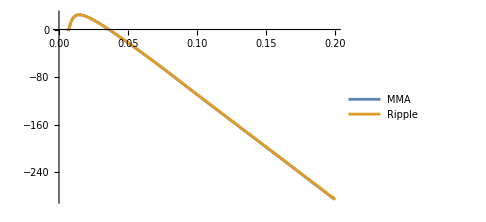
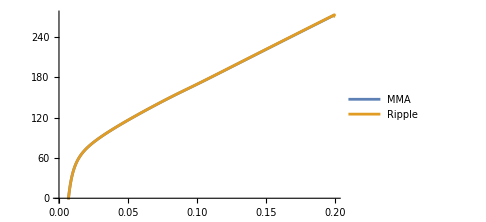
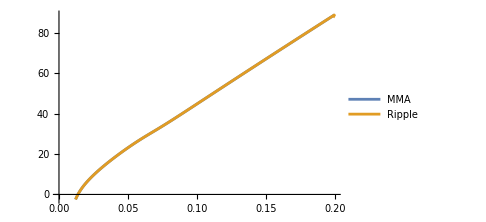
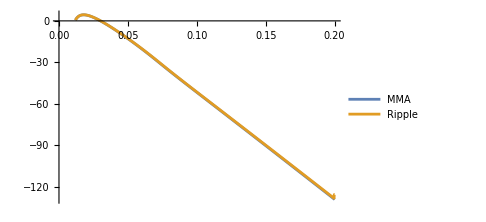
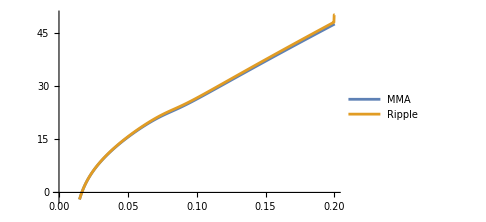
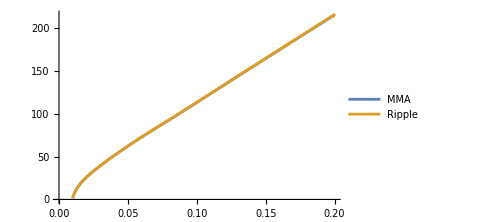
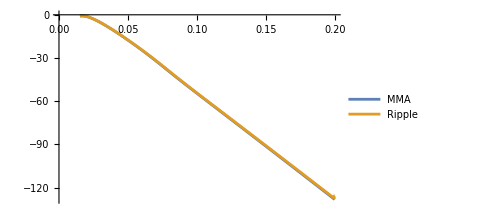
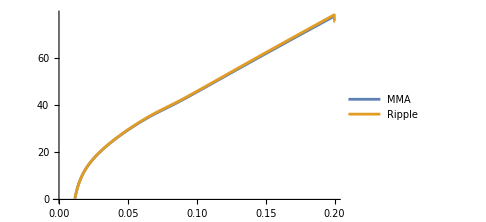

```mathematica
Table[ListLinePlot[test, PlotLegends->{"MMA", "Ripple"}, ImageSize->Medium ], {10}]
```

### Detailed Comparisons

"Ripple functions"  is a series of auxiliary definitions to do the detailed comparisons which are actually calculated in "Comparisons"

#### Ripple functions

```mathematica
helperCoeffs = ExternalFunction[python, "def Coeffs(theta):
	a = IMRD_utils.get_coeffs(theta)
	return np.array(a)"
];

RippleCoeffs[θ_] := helperCoeffs[θ]//Normal
```

```mathematica
helperTransitionFrequencies = ExternalFunction[python, "def transitionfrequencies(theta, gamma2, gamma3):
	a = IMRD_utils.get_transition_frequencies(theta, gamma2, gamma3)
	return np.array(a)
"];

RippleTransitionFrequencies[θ_, γ2_, γ3_] := helperTransitionFrequencies[θ, γ2, γ3]//Normal
```

```mathematica
helperInspiralPhase = ExternalFunction[python, "def InspiralPhase(f, theta, coeffs):
	a = np.array(f)
	return np.array(IMRD.get_inspiral_phase(a, theta, coeffs) )"];

RippleInspiralPhase[f_, θ_, coeffs_] := helperInspiralPhase[f, θ, coeffs]//Normal
```

```mathematica
helperIntPhase = ExternalFunction[python, "def IntPhase(f, theta, coeffs):
	a = np.array(f)
	return np.array(IMRD.get_IIa_raw_phase(a, theta, coeffs) )"];
	
RippleIntPhase[f_, θ_, coeffs_] := helperIntPhase[f, θ, coeffs]//Normal
```

```mathematica
helperMRPhase = ExternalFunction[python, "def MRPhase(f, theta, coeffs, fRD, fDAMP):
	a = np.array(f)
	return np.array(IMRD.get_IIb_raw_phase(a, theta, coeffs, fRD, fDAMP) )"];
	
RippleMRPhase[f_, θ_, coeffs_, fRD_,fDAMP_] := helperMRPhase[f, θ, coeffs, fRD, fDAMP]//Normal
```

```mathematica
helperTotalPhase = ExternalFunction[python, "def totalPhase(f, theta, coeffs, transition_frequencies):
	a = np.array(f)
	return np.array(IMRD.Phase(a, theta, coeffs, transition_frequencies) )"];
	
RippleTotalPhase[f_, θ_, coeffs_, transition_] := helperTotalPhase[f, θ, coeffs, transition]//Normal
```

#### Comparisons

```mathematica
CompareInspiral := Module[
	{f, θ = {0,0,0,0}, coeffs, χs, χa, η, pythonIns, MMA, InspiralPhase, 
	G = UnitConvert[("GravitationalConstant")/("SpeedOfLight")^3, ("Seconds")/("SolarMass")][[1]]}, 
	
	{θ[[1]], θ[[2]]} = ReverseSort@RandomReal[{10,100}, 2];
	η = (θ[[1]] θ[[2]])/(θ[[1]]+θ[[2]])^2;

	{θ[[3]], θ[[4]]} = RandomReal[{-1,1}, 2]; 
	χs = 1/2 (θ[[3]] + θ[[4]]); χa = 1/2 (θ[[3]] - θ[[4]]);
	
	f = Range[20., 2048., 0.25] (θ[[1]] + θ[[2]]) G;
	
	coeffs = RippleCoeffs[θ];
	
	pythonIns = RippleInspiralPhase[f, θ, coeffs];

	InspiralPhase  = NRules[["ϕIns"]][[1,2]];
	
	MMA = InspiralPhase[f, η, θ[[3]], θ[[4]]];
	
	Riffle[f, (pythonIns-MMA)/pythonIns]//Partition[#,2]&;

	{pythonIns, MMA}
	(*2 (pythonIns-MMA)/(pythonIns+MMA)*)
]
```

```mathematica
CompareInt := Module[
	{f, θ = {0,0,0,0}, coeffs, χs, χa, η, pythonInt, MMAInt,
	G = UnitConvert[("GravitationalConstant")/("SpeedOfLight")^3, ("Seconds")/("SolarMass")][[1]],
	χPN}, 
	
	
	{θ[[1]], θ[[2]]} = ReverseSort@RandomReal[{10,100}, 2]; η = (θ[[1]] θ[[2]])/(θ[[1]]+θ[[2]])^2;
	{θ[[3]], θ[[4]]} = RandomReal[{-1,1}, 2]; χs = 1/2 (θ[[3]] + θ[[4]]); χa = 1/2 (θ[[3]] - θ[[4]]);
	f = Range[20., 2048., 0.25] (θ[[1]]+ θ[[2]]) G;
	

	χPN = √(1- 4 η) (θ[[3]]  - θ[[4]])/2 + (1-(76 η)/113) (θ[[3]] + θ[[4]])/2;
	coeffs = RippleCoeffs[θ];
	
	pythonInt = RippleIntPhase[f, θ, coeffs];

	
	MMAInt = NRules["ϕInt"][[1,2]][f, η, χPN];
	
	(MMAInt - pythonInt)/pythonInt;
	{MMAInt, pythonInt}
]
```

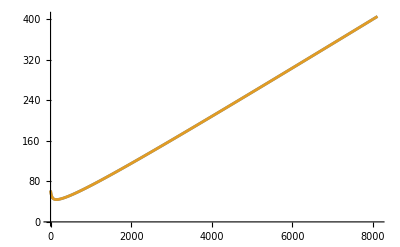
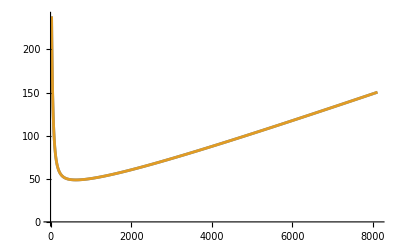
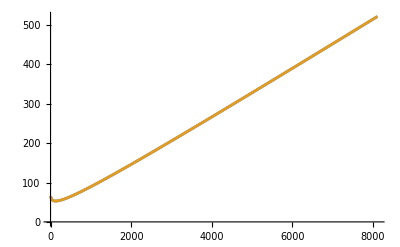
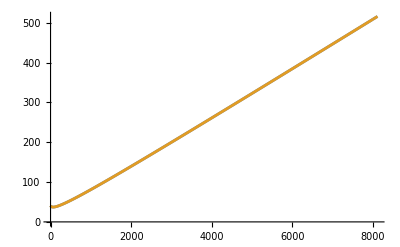
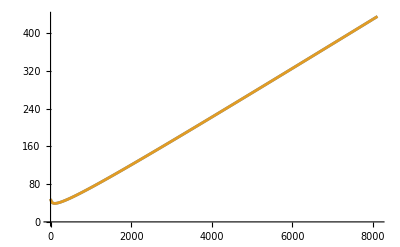
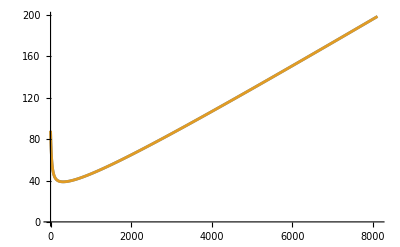
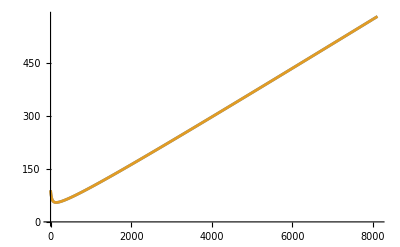
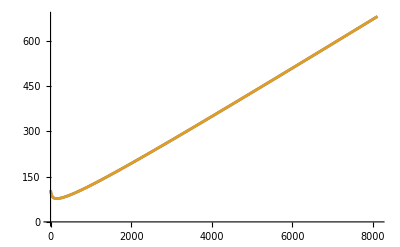

```mathematica
Table[ListLinePlot[CompareInt], {20}]
```

```mathematica
CompareMR := Module[
	{
		f, θ = {0,0,0,0}, coeffs, χs, χa, η, pythonIns, MMA, fRD, fDAMP, ωRD, ωDAMP,
		G = UnitConvert[("GravitationalConstant")/("SpeedOfLight")^3, ("Seconds")/("SolarMass")][[1]], χPN
	}, 
	
	{θ[[1]], θ[[2]]} = ReverseSort@RandomReal[{10,100}, 2]; η = (θ[[1]] θ[[2]])/(θ[[1]]+θ[[2]])^2;
	{θ[[3]], θ[[4]]} = RandomReal[{-1,1}, 2]; χs = 1/2 (θ[[3]] + θ[[4]]); χa = 1/2 (θ[[3]] - θ[[4]]);
	f = Range[20., 2048., 0.25] (θ[[1]]+ θ[[2]]) G;

	χPN = √(1- 4 η) (θ[[3]]  - θ[[4]])/2 + (1-(76 η)/113) (θ[[3]] + θ[[4]])/2;
	
	coeffs = RippleCoeffs[θ];
	{fRD, fDAMP} = (RippleTransitionFrequencies[θ, Sequence@@coeffs[[6;;7]]])[[-2;;-1]];
	
	pythonIns = RippleMRPhase[f, θ, coeffs, fRD, fDAMP];
	
	{ωRD, ωDAMP} =  G (θ[[1]] + θ[[2]] ) {fRD, fDAMP};
	
	MMA = NRules["ϕMR"][[1,2]][f, η, χPN, ωRD, ωDAMP,coeffs[[-1]]];
	
	(pythonIns - MMA)/pythonIns;
	{pythonIns, MMA}
]
```

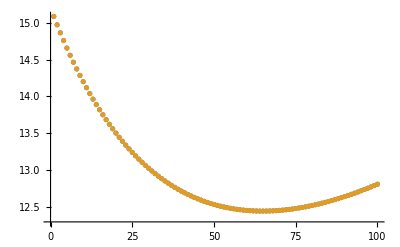
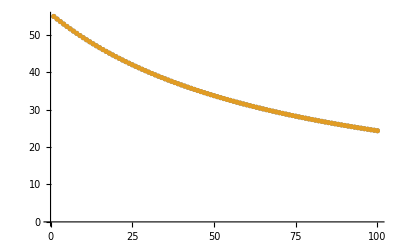
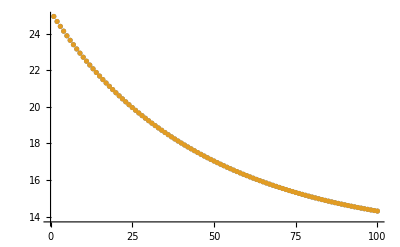
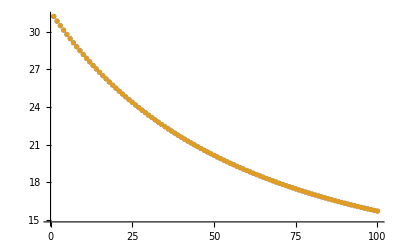
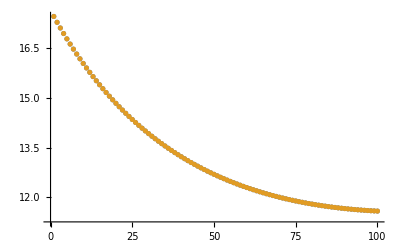
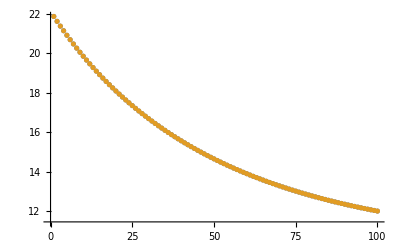
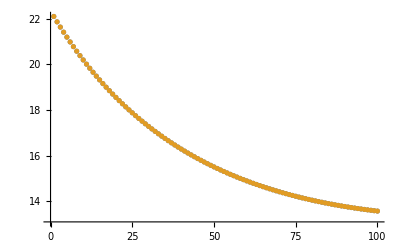
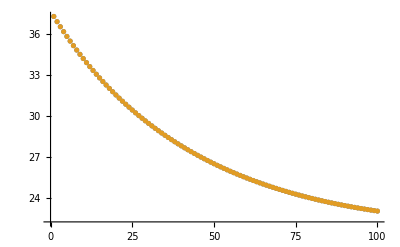

```mathematica
Table[ListPlot[CompareMR[[All, 1;;100]], PlotRange->All], 20]
```

```mathematica
ComparePhase := Module[
	{
	f,  coeffs,θ,  η, pythonPhase, MMA, fRD, fDAMP, transition, M,
	G = UnitConvert[("GravitationalConstant")/("SpeedOfLight")^3, ("Seconds")/("SolarMass")][[1]],  χPN, S, aeff, b, relativeDiff
	}, 

	θ = {0,0,0,0};
	{θ[[1]], θ[[2]]} = ReverseSort@RandomReal[{10,130}, 2]; {θ[[3]], θ[[4]]} = RandomReal[{-1,1}, 2];

	S =  1/4 (1 + √(1- 4 η))^2 θ[[3]] +1/4 (1-√(1-4 η))^2 θ[[4]];	
	χPN = √(1- 4 η) (θ[[3]]  - θ[[4]])/2 + (1-(76 η)/113) (θ[[3]] + θ[[4]])/2;
	aeff = S + 2 √3. η+(-0.085 S+0.102 S^2 - 1.355 S^3-0.868 S^4) η - 4.399 η^2+(-5.837 S-2.097 S^2+4.109 S^3+2.064 S^4) η^2+9.397 η^3-13.181 η^4;

	M = θ[[1]] + θ[[2]];  
	η = (θ[[1]] θ[[2]])/M^2;
	f = Range[20., 2048., 0.25] M G;

		
	coeffs = RippleCoeffs[θ];
	transition = RippleTransitionFrequencies[θ,  Sequence@@coeffs[[6;;7]] ];


	pythonPhase = RippleTotalPhase[f/(M G), θ, coeffs, transition];
	
	

	MMA = Quiet[Replace[ϕIMR[$f, $η, $χ1, $χ2, $χPN, $S], rulesList, Infinity], CompiledFunction::cfsa];
	
	MMA = MMA/.{$f-> f, $η->η, $χ1->θ[[3]], $χ2 ->θ[[4]], $S ->S, $χPN -> χPN};
	
	
	relativeDiff = 2 (MMA-pythonPhase)/(MMA+pythonPhase);

	(*Riffle[f, relativeDiff]//Partition[#,2]&*)
	{MMA, pythonPhase}

]
```

## Amplitude:

Now we can do the same construction for the amplitude, we start by recalling the variables:

```mathematica
NRules[#][[1,1]]&/@{"𝒜Ins", "𝒜Int", "𝒜MR"}
```

{𝒜Ins[ω_,η_,χ1_,χ2_],𝒜Int[ω_,ω3_,v1_,v2_,v3_,d1_,d3_],AMR[ω_,η_,χPN_,γ3ωDAMP_,ΔωRD_,γ2_]}

Recalling that:

```mathematica
"ω3 == ωPeak"
"v1 == 𝒜Ins[0.014,...]"
"v2==v2[η,χPN]"
"v3 = 𝒜MR[ω3,...]"
"d1== ∂_ω 𝒜Ins[0.014]"
"d3== ∂_ω 𝒜MR[ω3]"
"ΔωRD ==ω-ωRD"
```

ω3 == ωPeak

v1 == 𝒜Ins[0.014,...]

v2==v2[η,χPN]

v3 = 𝒜MR[ω3,...]

d1== ∂_ω 𝒜Ins[0.014]

d3== ∂_ω 𝒜MR[ω3]

ΔωRD ==ω-ωRD

Now, we can define:

```mathematica
𝒜IMR[f_, M_,  η_, χ1_, χ2_, dL_] = Module[
	{S, aeff, χPN,ringdownFrequency, DampingFrequency, gamma2, gamma3, ω3, v1,V2,v3, d1, d3, ω, c, G, ω2},
	
	(*We need a lot of definitions first:*)
	S =  1/4 (1 + √(1-4 η))^2 χ1 + 1/4 (1-√(1-4 η))^2 χ2;
	aeff = S + 2 √3. η + (-0.085 S + 0.102 S^2 - 1.355 S^3-0.868 S^4) η - 4.399 η^2+(-5.837 S-2.097 S^2+4.109 S^3+2.064 S^4) η^2+9.397 η^3-13.181 η^4;
	χPN = √(1- 4 η) (χ1-χ2)/2 + (1-(76 η)/113) (χ1+χ2)/2;
	ringdownFrequency = SF[η, S, ωRD[aeff]];
	DampingFrequency = SF[η, S, ωDAMP[aeff]];
	gamma2 = γ2[η, χPN];
	gamma3 = γ3[η, χPN];


	ω3 = ωPeak[ringdownFrequency, DampingFrequency, gamma2, gamma3];
	ω2 = (ω3+0.014)/2;
	v1 = 𝒜Ins[0.014, η, χ1, χ2];
	V2 = ω2^(-7/6) √η v2[η, χPN];
	v3 = AMR[ω3, η, χPN, gamma3 DampingFrequency, ω3 - ringdownFrequency, gamma2];
	d1 = $D[{1,0,0,0}, 𝒜Ins][0.014, η, χ1, χ2];
	d3 = (
		$D[{1,0,0,0,0,0},AMR][ω3, η, χPN, gamma3 DampingFrequency, ω3-ringdownFrequency, gamma2] +
		$D[{0,0,0,0,1,0}, AMR][ω3, η, χPN, gamma3 DampingFrequency, ω3-ringdownFrequency, gamma2]
	);


	G=UnitConvert[("GravitationalConstant")/("SpeedOfLight")^3, ("Seconds")/("SolarMass")][[1]];
	c = UnitConvert["SpeedOfLight", ("Megaparsecs")/("Seconds")][[1]];
	ω = M*f*G;

	(*Now, we can just write down the function:*)
	𝒜0 = √(5/6) c/(2 π^(2/3)) (M G)^2/dL;

	𝒜0*(
		𝒜Ins[ω, η, χ1, χ2] usθ[0.014-ω] + 
		𝒜Int[ω, ω3, v1,V2,v3,d1,d3] usθ[(ω-0.014) (ω3- ω)] + 
		AMR[ω,η,χPN,gamma3 DampingFrequency, ω-ringdownFrequency,gamma2] usθ[(ω-ω3) (0.2-ω)]
	)
]//Simplify[
	#,
	Assumptions-> 0<f && 0<η<1/4 && 0<M && -1<= χ1 <=1&&-1<= χ2 <=1,
	ComplexityFunction->ByteCount
	]&;
```

Now, we define some helper function to do the comparison:

```mathematica
helperCoeffs = ExternalFunction[python, "def Coeffs(theta):
	a = IMRD_utils.get_coeffs(theta)
	return np.array(a)"
];

RippleCoeffs[θ_] := helperCoeffs[θ]//Normal

helperArg = ExternalFunction[python, "def h0(f, θin, θextr, coeffs,  fref):
	b = np.array(f)
	a = IMRD._gen_IMRPhenomD(b, θin, θextr, coeffs,  fref)
	return np.array(a)"
];

Amplitude[f_, θin_,θex_, coeffs_, fref_] := Abs[helperArg[f, θin, θex, coeffs, fref]//Normal]
```

```mathematica
test𝒜 := Module[
	{f, M, χ1, χ2,pos, m1, m2,η, θ, Ripple, MMA, ω, θin, θex, coeffs,  
	G = UnitConvert[("GravitationalConstant")/("SpeedOfLight")^3, ("Seconds")/("SolarMass")][[1]]
	},

	f = Range[20, 4000,0.25];
	{m1, m2} = ReverseSort@RandomReal[{10,120},2];
	M = (m1+m2);
	η = (m1 m2)/M^2;
	{χ1, χ2} = RandomReal[{-1,1}, 2];
	ω = G M f;


	θex = {1, 0, 0};
	θin = {m1,m2, χ1, χ2};
	coeffs = RippleCoeffs[θin];

	Ripple = Amplitude[f, θin, θex, coeffs,  20];

	Ripple = Riffle[ω, Ripple]//Partition[#,2]&;
	
	MMA = Quiet[Replace[𝒜IMR[$a, M, η, χ1, χ2, 1], rulesList, Infinity]]/.rulesList;
	MMA = MMA/. $a ->f;

	MMA = Riffle[ω,MMA]//Partition[#,2]&;

	pos = FirstPosition[ω, x_/; x>=0.2]//Last; (*0.2 is the upper cutoff for IMRPhenomD. *)

	{MMA, Ripple}[[All, 1;;pos]]
]
```

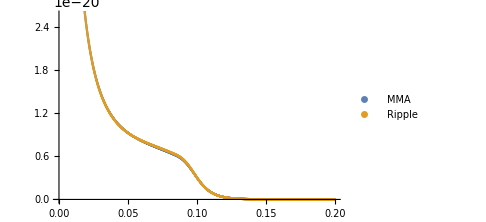
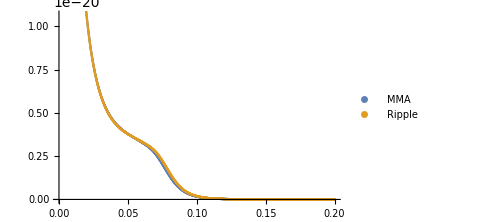
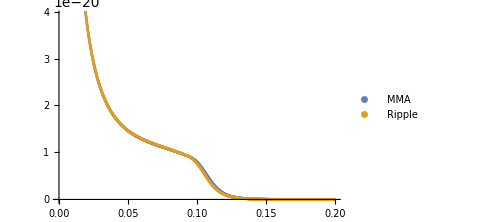
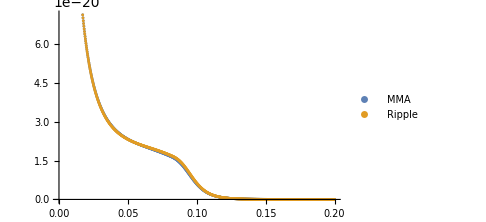
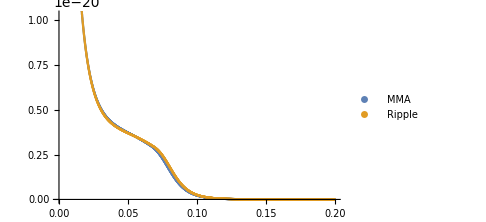

```mathematica
Table[ListPlot[Quiet[test𝒜], PlotLegends->{"MMA", "Ripple"}, ImageSize->Medium], {5}]
```

```mathematica
test =Simplify[𝒜IMR[f,M,η,χ1,χ2,1] Exp[-I Ψ[f,M,η,χ1,χ2,0,0,20]], ComplexityFunction->ByteCount];
```

```mathematica
a = D[test, {{M, η, χ1, χ2},1}]
```

```mathematica
D[a[[3]], {{ χ1, χ2}}]
```

$Aborted

```mathematica
Derivative[x__][y_Symbol][k__] := $D[{x}, y][k]
Derivative[x__][$D[y_List, s_Symbol]][k__] := $D[{x} + y, s][k]
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

FelipeBarbosa/SymDALI

FelipeBarbosa`SymDALI`

FelipeBarbosa/SymDALI/tutorial/IMRPhenomDDefs

### Keywords

$Aborted